## Driven qubits

```mathematica
(* Pauli Matrices *)
Clear[sx,sy,sz,s0];
sx = {{0,1},{1,0}};
sy = {{0,-ⅈ},{ⅈ,0}};
sz = {{1,0},{0,-1}};
s0 = {{1,0},{0,1}};
```

```mathematica
(* Hamiltonian *)
Clear[ω,γ];
Hamil = ω*sz + γ*sx;
V = Eigenvectors[Hamil];
V1 = Normalize[V[[1]]]
V2 =Normalize[V[[2]]]
V = {V1,V2};
V= Transpose[V];
FullSimplify[Inverse[V].Hamil.V]//MatrixForm
```

{-(-ω+√(γ^2+ω^2))/(γ √(1+Abs[(-ω+√(γ^2+ω^2))/γ]^2)),1/(√(1+Abs[(-ω+√(γ^2+ω^2))/γ]^2))}

{-(-ω-√(γ^2+ω^2))/(γ √(1+Abs[(-ω-√(γ^2+ω^2))/γ]^2)),1/(√(1+Abs[(-ω-√(γ^2+ω^2))/γ]^2))}

(-√(γ^2+ω^2) | 0
0 | √(γ^2+ω^2))

```mathematica
(* Unitarity *)
FullSimplify[Inverse[V].V]//MatrixForm
FullSimplify[V.Inverse[V]]//MatrixForm
Assuming[ω∈Reals && γ∈Reals,FullSimplify[Transpose[V].V]]//MatrixForm
Assuming[ω∈Reals && γ∈Reals,FullSimplify[V.Transpose[V]]]//MatrixForm
Assuming[ω∈Reals && γ∈Reals,FullSimplify[Abs[Det[V]]]]
Assuming[ω∈Reals && γ∈Reals,FullSimplify[Inverse[V] - Transpose[V]]]//MatrixForm
```

(1 | 0
0 | 1)

(1 | 0
0 | 1)

(1 | 0
0 | 1)

«1 more identical outputs»

1

(0 | 0
0 | 0)

```mathematica
(* Invariant Heat *)
Clear[V1,V2];
V1[α_,γ_] := {(α-√(α^2+γ^2))/(√(2*(γ^2+α^2-α √(α^2+γ^2)))),γ/(√(2*(γ^2+α^2-α √(α^2+γ^2))))};
V2[α_,γ_]:= {(α+√(α^2+γ^2))/(√(2*(γ^2+α^2+α √(α^2+γ^2)))),γ/(√(2*(γ^2+α^2+α √(α^2+γ^2))))};
```

```mathematica
FullSimplify[V1[1,γ].V2[1,γ]]
FullSimplify[V1[1,γ].V1[1,γ]]
FullSimplify[V2[1,γ].V1[1,γ]]
FullSimplify[V2[1,γ].V2[1,γ]]
FullSimplify[D[V1[1,γ],γ].V2[1,γ]]
FullSimplify[D[V2[1,γ],γ].V1[1,γ]]
FullSimplify[D[V1[1,γ],γ].V1[1,γ]]
FullSimplify[D[V2[1,γ],γ].V2[1,γ]]
```

0

1

0

1

-γ/(2 √(1+γ^2) √(1+γ^2-√(1+γ^2)) √(1+γ^2+√(1+γ^2)))

γ/(2 √(1+γ^2) √(1+γ^2-√(1+γ^2)) √(1+γ^2+√(1+γ^2)))

0

0

```mathematica
Eigenvalues[Hamil]
```

{-√(γ^2+ω^2),√(γ^2+ω^2)}

```mathematica
(* Dynamics of the density operator *)
Clear[ω,λ,γ,c11,c12,c21,c22,eps1,eps2,Z];
ω = 1;
ω0 = 1;
Ω = 1;
γ[x_] := Ω*Cos[ω0*x];
λ[x_] := Sqrt[ω^2+γ[x]^2];

(* Initial State *)
eps1[x_] := -√(ω^2+γ[x]^2);
eps2[x_] := √(ω^2+γ[x]^2);
β = 1.5;
Z[x_] := Exp[-β*eps1[x]]+Exp[-β*eps2[x]]; (* Partition function *)

eqns ={c11'[t] == -(ω*γ'[t])/(2*λ[t]^2)*(c12[t] + c21[t]),
c12'[t] == 2*ⅈ*λ[t]*c12[t]-(ω*γ'[t])/(2*λ[t]^2)*(c22[t] - c11[t]),
c21'[t] == -2*ⅈ*λ[t]*c21[t]-(ω*γ'[t])/(2*λ[t]^2)*(c22[t] - c11[t]),
c22'[t] == (ω*γ'[t])/(2*λ[t]^2)*(c12[t] + c21[t]),
(* c11[0] == Exp[-β*eps1[0]]/Z[0], c22[0] == Exp[-β*eps2[0]]/Z[0], c12[0] == 0, c21[0] == 0 *)
c11[0] == 1, c22[0] == 0, c12[0] == 0, c21[0] == 0};
 sol = NDSolve[eqns,{c11,c12, c21, c22},{t,50}];
fc11 = c11/.sol[[1,1]];
fc12 = c12/.sol[[1,2]];
fc21 = c21/.sol[[1,3]];
fc22 = c22/.sol[[1,4]];
```

```mathematica
(* Work, Heat and Coherences *)
Clear[work,heat,cohentro,entro];
work = {};
heat = {};
cohentro = {};
entroS = {};
entroF = {};
entroC = {};
For[t0 = 0, t0 ≤ 50, 
(* Heat *)
heat0 = NIntegrate[2*Re[fc12[x]]*γ'[x]/λ[x],{x,0,t0}];
heat = Append[heat,{t0,Re[heat0]}];

(* Work *)
work0 = NIntegrate[(fc22[x] - fc11[x])*(γ[x]*γ'[x])/λ[x],{x,0,t0}];
work = Append[work,{t0,Re[work0]}];

(* Coherences *)
eig1 = 0.5 + 0.5*Sqrt[1 - 4*(fc11[t0]*fc22[t0]-fc21[t0]*fc12[t0])];
eig2 = 0.5 - 0.5*Sqrt[1 - 4*(fc11[t0]*fc22[t0]-fc21[t0]*fc12[t0])];
coh0 = -fc11[t0]*Log[2,fc11[t0]]-fc22[t0]*Log[2,fc22[t0]]+eig1*Log[2,eig1]+eig2*Log[2,eig2];
cohentro = Append[cohentro,{t0,Re[coh0]}];

(* Entropy production - Two forms 
rhoS = {{fc11[t0],fc12[t0]},{fc21[t0],fc22[t0]}};
rhoβ = {{Exp[-β*eps1[t0]]/Z[t0],0},{0,Exp[-β*eps2[t0]]/Z[t0]}};
S0 = Tr[rhoS.MatrixLog[rhoS]] - Tr[rhoS.MatrixLog[rhoβ]];
entroS = Append[entroS,{t0,Re[S0]}];

S0 = β*work0 - (-Log[Z[t0]] + Log[Z[0]]);
entroF = Append[entroF,{t0,Re[S0]}];

(* Classical entropy production *)
entroC0 = fc11[t0]*Log[fc11[t0]] + fc22[t0]*Log[fc22[t0]]  -fc11[t0]*Log[rhoβ[[1,1]]] - fc22[t0]*Log[rhoβ[[2,2]]]; 
entroC = Append[entroC,{t0,Re[entroC0]}];
*)
t0 = t0+0.1];
```

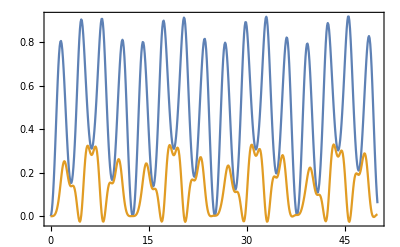

```mathematica
ListPlot[{work,heat},PlotRange->All,Frame->True,Joined->True]
```

```mathematica
Export["/home/lucas/Downloads/work_cos.txt",work,"CSV"];
Export["/home/lucas/Downloads/heat_cos.txt",heat,"CSV"];
Export["/home/lucas/Downloads/coh_cos.txt",cohentro,"CSV"];
Export["/home/lucas/Downloads/entroF_cos.txt",entroF,"CSV"];
Export["/home/lucas/Downloads/entroS_cos.txt",entroS,"CSV"];
Export["/home/lucas/Downloads/entroC_cos.txt",entroC,"CSV"];
```

## Qubits under noisy channels

```mathematica
Clear[p,γ];

(* Krauss Operators - Generalized Amplitude Damping *)
Γgad0[p_,γ_] := Sqrt[γ]*{{1,0},{0,Sqrt[1-p]}};
Γgad1[p_,γ_] := Sqrt[γ]*{{0,Sqrt[p]},{0,0}};
Γgad2[p_,γ_] := Sqrt[1-γ]*{{Sqrt[1-p],0},{0,1}};
Γgad3[p_,γ_] := Sqrt[1-γ]*{{0,0},{Sqrt[p],0}};

(* Krauss Operators - Dephasing *)
Γd0[p_] := Sqrt[p/2]*s0;
Γd1[p_] := Sqrt[1-p/2]*sz;

(* Krauss Operators - Bit-flip *)
Γbf0[p_] := Sqrt[p]*sx;
Γbf1[p_] := Sqrt[1-p]*s0;

(* Initial Density Matrix *)
rho0 = {{r00,r01},{r10,1-r00}};
```

```mathematica
Hamil = α*sz + γ*sx
```

{{α,γ},{γ,-α}}

```mathematica
V = Eigenvectors[Hamil]
```

{{-(-α+√(α^2+γ^2))/γ,1},{-(-α-√(α^2+γ^2))/γ,1}}

```mathematica
FullSimplify[Inverse[Transpose[V]].Hamil.Transpose[V]]//MatrixForm
```

(-√(α^2+γ^2) | 0
0 | √(α^2+γ^2))

```mathematica
V1 = Normalize[{-(-α+√(α^2+γ^2))/γ,1}];
V2 = Normalize[{-(-α-√(α^2+γ^2))/γ,1}];
```

```mathematica
sx.sz//MatrixForm
```

(0 | -1
1 | 0)

```mathematica
V1
```

{-(-α+√(α^2+γ^2))/(γ √(1+Abs[(-α+√(α^2+γ^2))/γ]^2)),1/(√(1+Abs[(-α+√(α^2+γ^2))/γ]^2))}

```mathematica
Eigenvalues[Hamil]
```

{-√(α^2+γ^2),√(α^2+γ^2)}

```mathematica
(* Evolved states under the channels *)
```

```mathematica
rhotgad[p_,γ_] := Γgad0[p,γ].rho0.Transpose[Γgad0[p,γ]] + Γgad1[p,γ].rho0.Transpose[Γgad1[p,γ]] + Γgad2[p,γ].rho0.Transpose[Γgad2[p,γ]] + Γgad3[p,γ].rho0.Transpose[Γgad3[p,γ]];
rhotd[p_] := Γd0[p].rho0.Transpose[Γd0[p]] + Γd1[p].rho0.Transpose[Γd1[p]]; rhotbf[p_] := Γbf0[p].rho0.Transpose[Γbf0[p]] + Γbf1[p].rho0.Transpose[Γbf1[p]];
```

```mathematica
(* Invariant heat *)
QinvGAD =
```

```mathematica
FullSimplify[Tr[α*λ*Exp[-λ*t]*D[rhotgad[p,γ],p].sz]]
```

```mathematica
V = FullSimplify[Eigenvectors[Hamil]];
```

```mathematica
NV = Transpose[{V1,V2}];
FullSimplify[Inverse[NV].Hamil.NV]
```

{{-√(α^2+β^2+γ^2),0},{0,√(α^2+β^2+γ^2)}}

```mathematica
FullSimplify[Inverse[V].V]
```

{{1,0},{0,1}}

```mathematica
FullSimplify[NV.Inverse[NV]]
```

{{1,0},{0,1}}

```mathematica
rho = {{r00,r01},{r10,1-r00}};
```

```mathematica
Mz = FullSimplify[rho.NV.sz.Inverse[NV],Element[α, Reals]&&Element[β, Reals]&&Element[γ, Reals]&&Element[λ, Reals]]
```

{{-α/(√(α^2+β^2+γ^2)),(-β+ⅈ γ)/(√(α^2+β^2+γ^2))},{-(β+ⅈ γ)/(√(α^2+β^2+γ^2)),α/(√(α^2+β^2+γ^2))}}

```mathematica
Ut = Cos[R]*s0 - ⅈ*(Rx*sx + Ry*sy + Rz*sz)*Sin[R];
(* rho0 = {{a,b},{c,d}}; *)
```

```mathematica
M = FullSimplify[Inverse[Ut].Mz.Ut, Element[R, Reals]&&Element[Rx, Reals]&&Element[Ry, Reals]&&Element[Rz, Reals]]
```

{{(-α Cos[R]^2+(Rx^2 α+Ry^2 α-Rz^2 α-2 Rx Rz β-2 Ry Rz γ) Sin[R]^2+(-Ry β+Rx γ) Sin[2 R])/(√(α^2+β^2+γ^2) (Cos[R]^2+(Rx^2+Ry^2+Rz^2) Sin[R]^2)),(-(β-ⅈ γ) Cos[R]^2-2 (Rx-ⅈ Ry) Rz α Sin[R]^2+((-(Rx-ⅈ Ry)^2+Rz^2) β-ⅈ ((Rx-ⅈ Ry)^2+Rz^2) γ) Sin[R]^2+(ⅈ Rx α+Ry α-ⅈ Rz β-Rz γ) Sin[2 R])/(√(α^2+β^2+γ^2) (Cos[R]^2+(Rx^2+Ry^2+Rz^2) Sin[R]^2))},{(-(β+ⅈ γ) Cos[R]^2-2 (Rx+ⅈ Ry) Rz α Sin[R]^2+((-(Rx+ⅈ Ry)^2+Rz^2) β+ⅈ ((Rx+ⅈ Ry)^2+Rz^2) γ) Sin[R]^2+(-ⅈ Rx α+Ry α+ⅈ Rz β-Rz γ) Sin[2 R])/(√(α^2+β^2+γ^2) (Cos[R]^2+(Rx^2+Ry^2+Rz^2) Sin[R]^2)),(α Cos[R]^2-2 Rx γ Cos[R] Sin[R]+(-Rx^2 α-Ry^2 α+Rz^2 α+2 Rx Rz β+2 Ry Rz γ) Sin[R]^2+Ry β Sin[2 R])/(√(α^2+β^2+γ^2) (Cos[R]^2+(Rx^2+Ry^2+Rz^2) Sin[R]^2))}}

```mathematica
(-α Cos[R]^2+(Rx^2 α+Ry^2 α-Rz^2 α-2 Rx Rz β-2 Ry Rz γ) Sin[R]^2+(-Ry β+Rx γ) Sin[2 R])/(√(α^2+β^2+γ^2) )
```

```mathematica
VT = {1/(√(α^2+β^2+γ^2))(-α Cos[R]^2-2 Ry √((β^2+γ^2)/(α^2+β^2+γ^2)) √(α^2+β^2+γ^2) Cos[R] Sin[R]+(Rx^2 α+(Ry-Rz) (Ry+Rz) α-2 Rx Rz √((β^2+γ^2)/(α^2+β^2+γ^2)) √(α^2+β^2+γ^2)) Sin[R]^2),(Cos[R]+ⅈ Rz Sin[R]) (((ⅈ Rx+Ry) α Sin[R])/(√(α^2+β^2+γ^2))-√((β^2+γ^2)/(α^2+β^2+γ^2)) (Cos[R]+ⅈ Rz Sin[R]))-ⅈ (Rx-ⅈ Ry) Sin[R] ((-ⅈ Rx-Ry) √((β^2+γ^2)/(α^2+β^2+γ^2)) Sin[R]-(α (Cos[R]+ⅈ Rz Sin[R]))/(√(α^2+β^2+γ^2)))}
```

```mathematica
FullSimplify[VT[[1]]]
```

1/(√(α^2+β^2+γ^2))(-α Cos[R]^2-2 Ry √((β^2+γ^2)/(α^2+β^2+γ^2)) √(α^2+β^2+γ^2) Cos[R] Sin[R]+(Rx^2 α+(Ry-Rz) (Ry+Rz) α-2 Rx Rz √((β^2+γ^2)/(α^2+β^2+γ^2)) √(α^2+β^2+γ^2)) Sin[R]^2)

```mathematica
FullSimplify[1/(√(α^2+β^2+γ^2))(-α Cos[R]^2-2 Ry √((β^2+γ^2)/1)  Cos[R] Sin[R]+(Rx^2 α+(Ry-Rz) (Ry+Rz) α-2 Rx Rz √((β^2+γ^2)/1) ) Sin[R]^2)]
```

1/(√(α^2+β^2+γ^2))(-α Cos[R]^2-2 Ry √(β^2+γ^2) Cos[R] Sin[R]+(Rx^2 α+(Ry-Rz) (Ry+Rz) α-2 Rx Rz √(β^2+γ^2)) Sin[R]^2)

```mathematica
M = M1.];
```

```mathematica
FullSimplify[Tr[M]]
```

$Aborted

```mathematica
D[Sqrt[1+x^2],x]
```

x/(√(1+x^2))